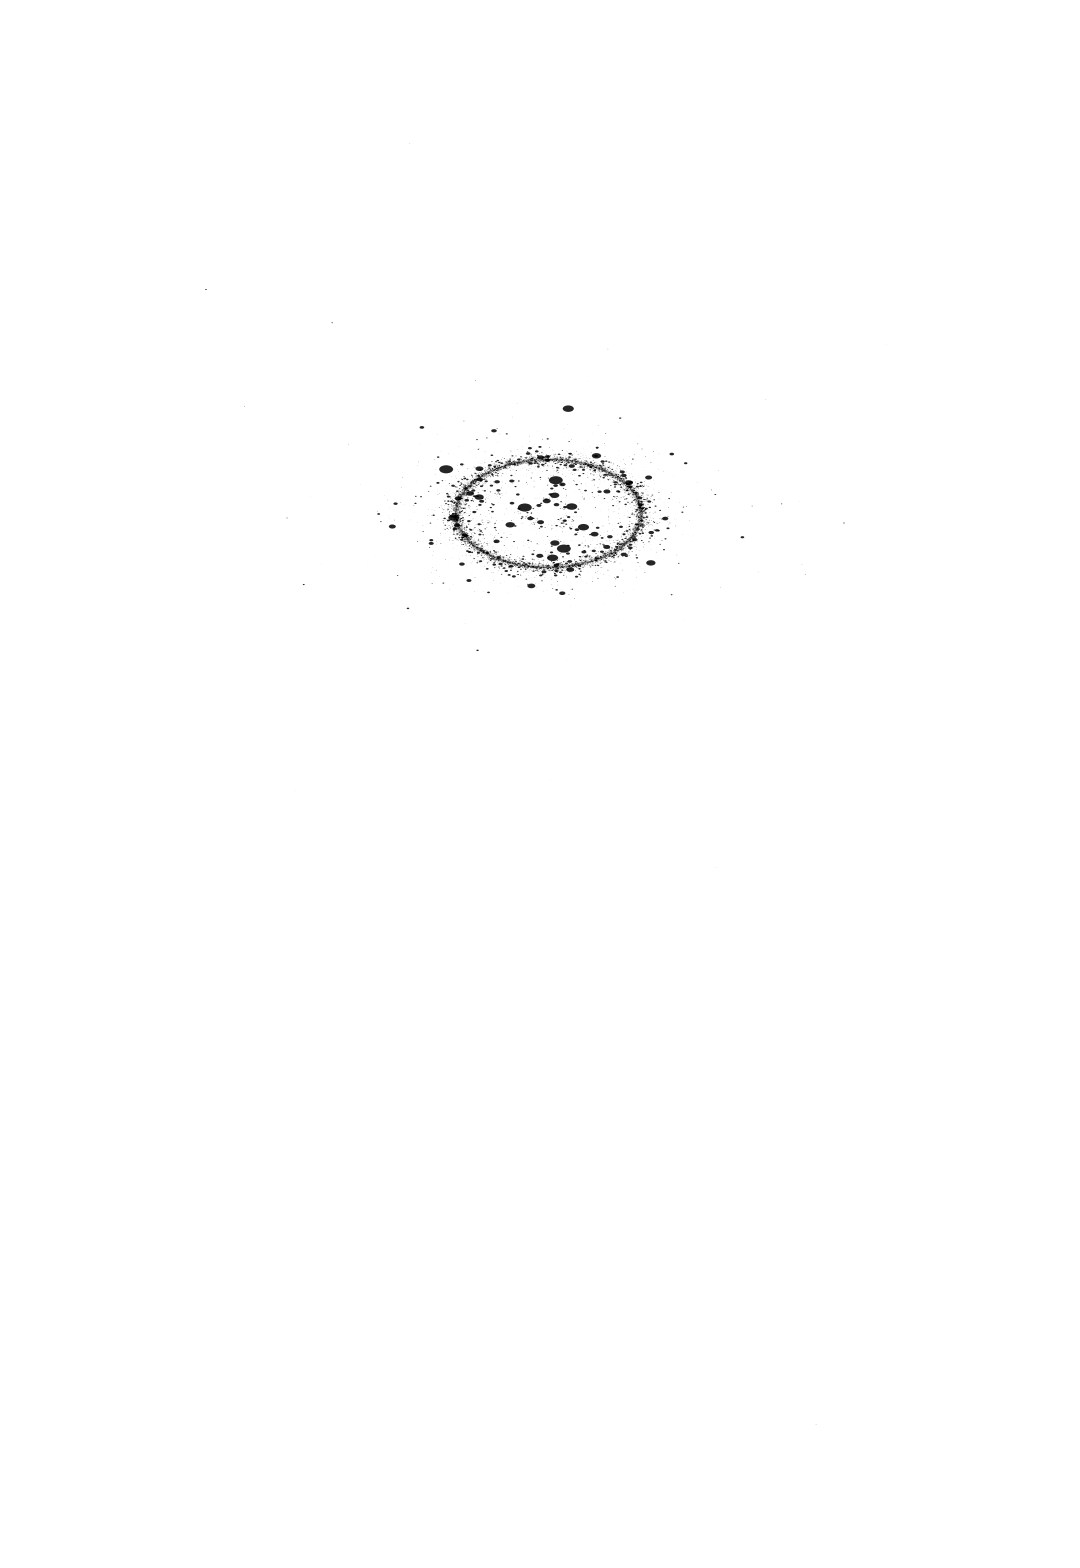

```mathematica
ClearAll["`*"]
SeedRandom[7];
coef[n_,k_]:=coef[n,k]=(RandomReal[{-1,1}]+RandomReal[{-1,1}] I);
nframes=240;
solve[theta_,n_]:=NSolve[Sum[coef[n,k] z^k,{k,1,n}]+0.2 E^(I theta)+0.9 E^(I 2 theta) z^3 If[n>=3,1,0]+0.9 E^(I 3 theta) z^6 If[n>=6,1,0]==0,z]
ClearAll[disks];
disks[theta_,n_]:=Disk@@@Flatten[Table[{{Re[z],Im[z]},Max[0.3/n,0.001]}/. solve[theta,n],{n,4,200}],1];
Graphics[{Black,Opacity[.85],disks[0,n]},PlotRange->1.3,ImageSize->1080]
```

```mathematica
frames=ParallelTable[Graphics[{Black,Opacity[.85],disks[theta,n]},PlotRange->1.3,ImageSize->1080],{theta,0,2 Pi (1-1/nframes),2 Pi/nframes}];//AbsoluteTiming
```

{34.1257,Null}

```mathematica
Parallelize@FrameListVideo[frames,RasterSize->1080,FrameRate->30]
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.